```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210603_bar_charts_and_OR_model"];
```

Fixed Boundaries (Initial Obj. Func. Term Series)

Data Input

```mathematica
modularityvalues12m4p4=Import["plot_values/fxd_bounds/(-20,20)-modularityvalues-fss.mx"];
modularityvalues12m1p1=Import["plot_values/fxd_bounds/(-5,5)-modularityvalues-fss.mx"];
modularityvalues12m2m4=Import["plot_values/fxd_bounds/(-10,-20)-modularityvalues-fss.mx"];
modularityvalues12p2p4=Import["plot_values/fxd_bounds/(10,20)-modularityvalues-fss.mx"];

modularityvalues32m4p4=Import["plot_values/fxd_bounds/(-20,20)-modularityvalues-fbs.mx"];
modularityvalues32m1p1=Import["plot_values/fxd_bounds/(-5,5)-modularityvalues-fbs.mx"];
modularityvalues32m2m4=Import["plot_values/fxd_bounds/(-10,-20)-modularityvalues-fbs.mx"];
modularityvalues32p2p4=Import["plot_values/fxd_bounds/(10,20)-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues12m4p4=Import["plot_values/fxd_bounds/(-20,20)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m4p4=Import["plot_values/fxd_bounds/(-20,20)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m1p1=Import["plot_values/fxd_bounds/(-5,5)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m1p1=Import["plot_values/fxd_bounds/(-5,5)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m2m4=Import["plot_values/fxd_bounds/(-10,-20)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m2m4=Import["plot_values/fxd_bounds/(-10,-20)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12p2p4=Import["plot_values/fxd_bounds/(10,20)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12p2p4=Import["plot_values/fxd_bounds/(10,20)-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues32m4p4=Import["plot_values/fxd_bounds/(-20,20)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m4p4=Import["plot_values/fxd_bounds/(-20,20)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m1p1=Import["plot_values/fxd_bounds/(-5,5)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m1p1=Import["plot_values/fxd_bounds/(-5,5)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m2m4=Import["plot_values/fxd_bounds/(-10,-20)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m2m4=Import["plot_values/fxd_bounds/(-10,-20)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32p2p4=Import["plot_values/fxd_bounds/(10,20)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32p2p4=Import["plot_values/fxd_bounds/(10,20)-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores12m4p4=Import["plot_values/fxd_bounds/(-20,20)-zscores-fss.mx"];
zscores12m1p1=Import["plot_values/fxd_bounds/(-5,5)-zscores-fss.mx"];
zscores12m2m4=Import["plot_values/fxd_bounds/(-10,-20)-zscores-fss.mx"];
zscores12p2p4=Import["plot_values/fxd_bounds/(10,20)-zscores-fss.mx"];

zscores32m4p4=Import["plot_values/fxd_bounds/(-20,20)-zscores-fbs.mx"];
zscores32m1p1=Import["plot_values/fxd_bounds/(-5,5)-zscores-fbs.mx"];
zscores32m2m4=Import["plot_values/fxd_bounds/(-10,-20)-zscores-fbs.mx"];
zscores32p2p4=Import["plot_values/fxd_bounds/(10,20)-zscores-fbs.mx"];
```

```mathematica
deletionrange=Range[0,450,50]
```

{0,50,100,150,200,250,300,350,400,450}

```mathematica
modularityvalues12={Thread[{deletionrange,modularityvalues12m4p4}],Thread[{deletionrange,modularityvalues12m1p1}],Thread[{deletionrange,modularityvalues12m2m4}],Thread[{deletionrange,modularityvalues12p2p4}]};
modularityvalues32={Thread[{deletionrange,modularityvalues32m4p4}],Thread[{deletionrange,modularityvalues32m1p1}],Thread[{deletionrange,modularityvalues32m2m4}],Thread[{deletionrange,modularityvalues32p2p4}]};
```

```mathematica
singlerandommodularityvalues12={Thread[{deletionrange,singlerandomerdrenmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12p2p4}]};
singlerandommodularityvalues32={Thread[{deletionrange,singlerandomerdrenmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32p2p4}]};
```

```mathematica
zscores12={Thread[{deletionrange,zscores12m4p4[[All,1]]}],Thread[{deletionrange,zscores12m4p4[[All,2]]}],Thread[{deletionrange,zscores12m1p1[[All,1]]}],Thread[{deletionrange,zscores12m1p1[[All,2]]}],Thread[{deletionrange,zscores12m2m4[[All,1]]}],Thread[{deletionrange,zscores12m2m4[[All,2]]}],Thread[{deletionrange,zscores12p2p4[[All,1]]}],Thread[{deletionrange,zscores12p2p4[[All,2]]}]};
zscores32={Thread[{deletionrange,zscores32m4p4[[All,1]]}],Thread[{deletionrange,zscores32m4p4[[All,2]]}],Thread[{deletionrange,zscores32m1p1[[All,1]]}],Thread[{deletionrange,zscores32m1p1[[All,2]]}],Thread[{deletionrange,zscores32m2m4[[All,1]]}],Thread[{deletionrange,zscores32m2m4[[All,2]]}],Thread[{deletionrange,zscores32p2p4[[All,1]]}],Thread[{deletionrange,zscores32p2p4[[All,2]]}]};
```

Plots

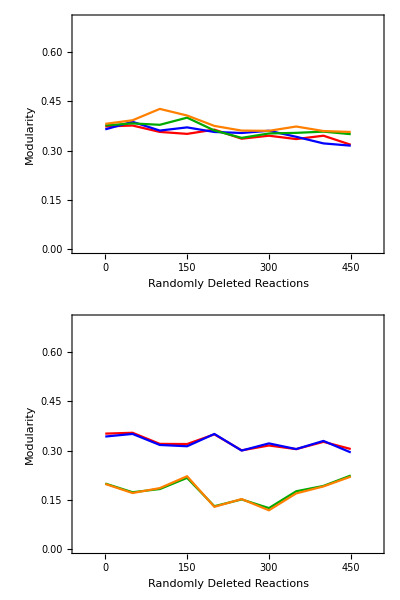
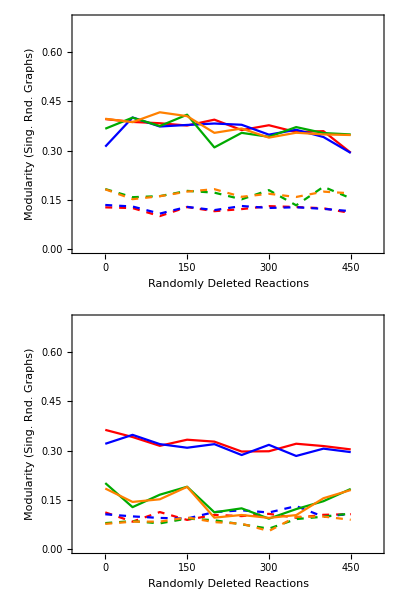
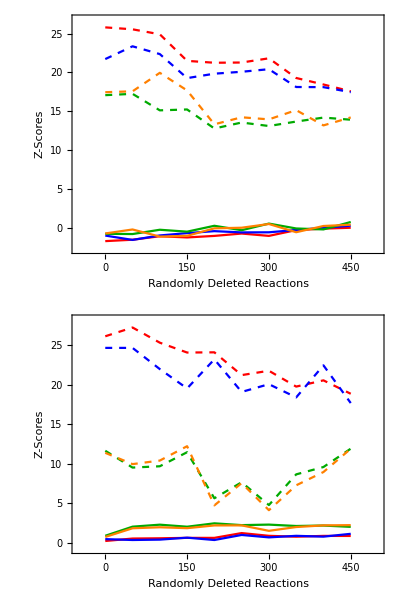

```mathematica
padding=38;
modularityplotrange={0,0.7};
xaxisplotrange={-50,500};
Row[{
Column[{ListLinePlot[modularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[modularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[singlerandommodularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores12m1p1,zscores12m2m4,zscores12m4p4,zscores12p2p4}],1]}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores32m1p1,zscores32m2m4,zscores32m4p4,zscores32p2p4}],1]}]}]
,Column[{LineLegend[{Darker@Green,Blue,Orange,Red},{"(-20,-10)","(-5,5)","(10,20)","(-20,20)"},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Objective Function\nCoefficient Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

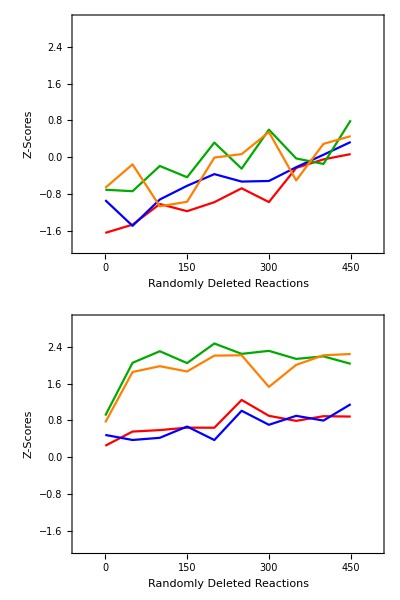

```mathematica
Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}]}]
```

Objective Function Terms Increased by 10%

Objective Function Intervals: (-4,4), (-1,1), (-2,-4), (2,4)

Data Input

```mathematica
modularityvalues12m4p4=Import["plot_values/10per_inc_obj-funcs/(-4,4)-modularityvalues-fss.mx"];
modularityvalues12m1p1=Import["plot_values/10per_inc_obj-funcs/(-1,1)-modularityvalues-fss.mx"];
modularityvalues12m2m4=Import["plot_values/10per_inc_obj-funcs/(-2,-4)-modularityvalues-fss.mx"];
modularityvalues12p2p4=Import["plot_values/10per_inc_obj-funcs/(2,4)-modularityvalues-fss.mx"];

modularityvalues32m4p4=Import["plot_values/10per_inc_obj-funcs/(-4,4)-modularityvalues-fbs.mx"];
modularityvalues32m1p1=Import["plot_values/10per_inc_obj-funcs/(-1,1)-modularityvalues-fbs.mx"];
modularityvalues32m2m4=Import["plot_values/10per_inc_obj-funcs/(-2,-4)-modularityvalues-fbs.mx"];
modularityvalues32p2p4=Import["plot_values/10per_inc_obj-funcs/(2,4)-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues12m4p4=Import["plot_values/10per_inc_obj-funcs/(-4,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m4p4=Import["plot_values/10per_inc_obj-funcs/(-4,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m1p1=Import["plot_values/10per_inc_obj-funcs/(-1,1)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m1p1=Import["plot_values/10per_inc_obj-funcs/(-1,1)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m2m4=Import["plot_values/10per_inc_obj-funcs/(-2,-4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m2m4=Import["plot_values/10per_inc_obj-funcs/(-2,-4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12p2p4=Import["plot_values/10per_inc_obj-funcs/(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12p2p4=Import["plot_values/10per_inc_obj-funcs/(2,4)-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues32m4p4=Import["plot_values/10per_inc_obj-funcs/(-4,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m4p4=Import["plot_values/10per_inc_obj-funcs/(-4,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m1p1=Import["plot_values/10per_inc_obj-funcs/(-1,1)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m1p1=Import["plot_values/10per_inc_obj-funcs/(-1,1)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m2m4=Import["plot_values/10per_inc_obj-funcs/(-2,-4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m2m4=Import["plot_values/10per_inc_obj-funcs/(-2,-4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32p2p4=Import["plot_values/10per_inc_obj-funcs/(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32p2p4=Import["plot_values/10per_inc_obj-funcs/(2,4)-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores12m4p4=Import["plot_values/10per_inc_obj-funcs/(-4,4)-zscores-fss.mx"];
zscores12m1p1=Import["plot_values/10per_inc_obj-funcs/(-1,1)-zscores-fss.mx"];
zscores12m2m4=Import["plot_values/10per_inc_obj-funcs/(-2,-4)-zscores-fss.mx"];
zscores12p2p4=Import["plot_values/10per_inc_obj-funcs/(2,4)-zscores-fss.mx"];

zscores32m4p4=Import["plot_values/10per_inc_obj-funcs/(-4,4)-zscores-fbs.mx"];
zscores32m1p1=Import["plot_values/10per_inc_obj-funcs/(-1,1)-zscores-fbs.mx"];
zscores32m2m4=Import["plot_values/10per_inc_obj-funcs/(-2,-4)-zscores-fbs.mx"];
zscores32p2p4=Import["plot_values/10per_inc_obj-funcs/(2,4)-zscores-fbs.mx"];
```

```mathematica
deletionrange=Range[0,450,50]
```

{0,50,100,150,200,250,300,350,400,450}

```mathematica
modularityvalues12={Thread[{deletionrange,modularityvalues12m4p4}],Thread[{deletionrange,modularityvalues12m1p1}],Thread[{deletionrange,modularityvalues12m2m4}],Thread[{deletionrange,modularityvalues12p2p4}]};
modularityvalues32={Thread[{deletionrange,modularityvalues32m4p4}],Thread[{deletionrange,modularityvalues32m1p1}],Thread[{deletionrange,modularityvalues32m2m4}],Thread[{deletionrange,modularityvalues32p2p4}]};
```

```mathematica
singlerandommodularityvalues12={Thread[{deletionrange,singlerandomerdrenmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12p2p4}]};
singlerandommodularityvalues32={Thread[{deletionrange,singlerandomerdrenmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32p2p4}]};
```

```mathematica
zscores12={Thread[{deletionrange,zscores12m4p4[[All,1]]}],Thread[{deletionrange,zscores12m4p4[[All,2]]}],Thread[{deletionrange,zscores12m1p1[[All,1]]}],Thread[{deletionrange,zscores12m1p1[[All,2]]}],Thread[{deletionrange,zscores12m2m4[[All,1]]}],Thread[{deletionrange,zscores12m2m4[[All,2]]}],Thread[{deletionrange,zscores12p2p4[[All,1]]}],Thread[{deletionrange,zscores12p2p4[[All,2]]}]};
zscores32={Thread[{deletionrange,zscores32m4p4[[All,1]]}],Thread[{deletionrange,zscores32m4p4[[All,2]]}],Thread[{deletionrange,zscores32m1p1[[All,1]]}],Thread[{deletionrange,zscores32m1p1[[All,2]]}],Thread[{deletionrange,zscores32m2m4[[All,1]]}],Thread[{deletionrange,zscores32m2m4[[All,2]]}],Thread[{deletionrange,zscores32p2p4[[All,1]]}],Thread[{deletionrange,zscores32p2p4[[All,2]]}]};
```

Plots

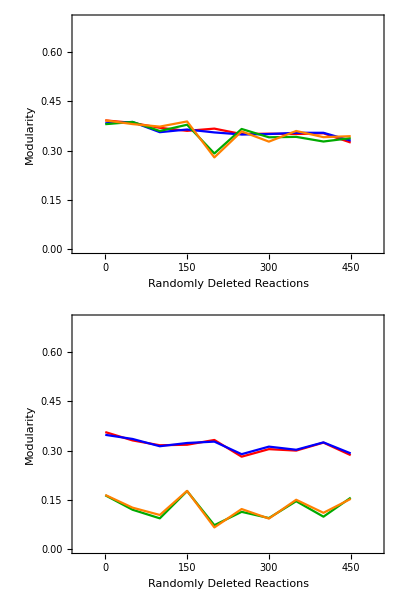
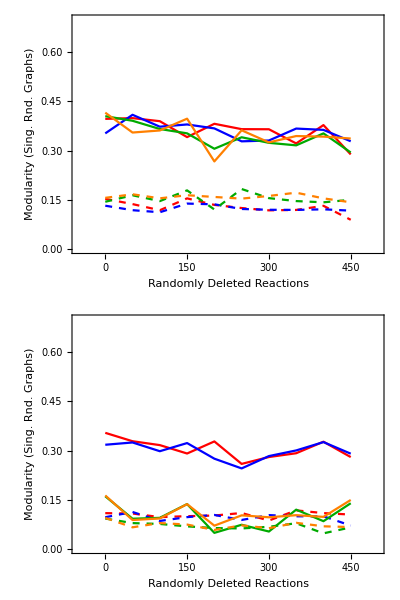
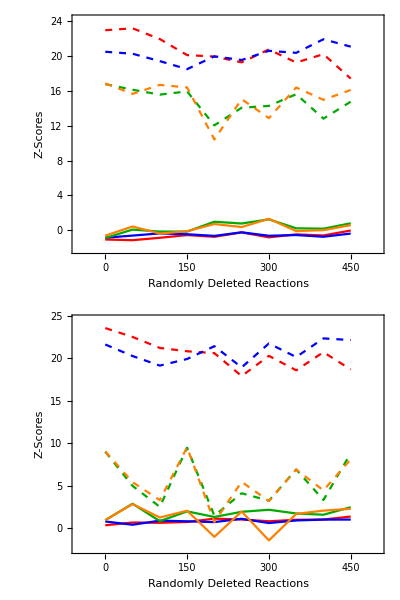

```mathematica
padding=38;
modularityplotrange={0,0.7};
xaxisplotrange={-50,500};
Row[{
Column[{ListLinePlot[modularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[modularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[singlerandommodularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores12m1p1,zscores12m2m4,zscores12m4p4,zscores12p2p4}],1]}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores32m1p1,zscores32m2m4,zscores32m4p4,zscores32p2p4}],1]}]}]
,Column[{LineLegend[{Darker@Green,Blue,Orange,Red},{"(-4,-2)","(-1,1)","(2,4)","(-4,4)"},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Objective Function\nCoefficient Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

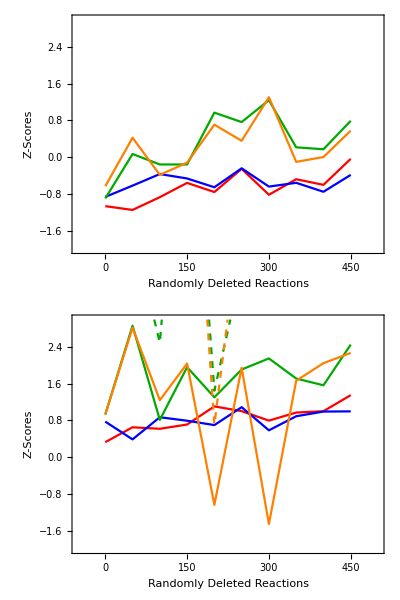

```mathematica
Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}]}]
```

Objective Function Terms Reduced by Half

Objective Function Intervals: (-4,4), (-1,1), (-2,-4), (2,4)

Data Input

```mathematica
modularityvalues12m4p4=Import["plot_values/half_obj-funcs/(-4,4)-modularityvalues-fss.mx"];
modularityvalues12m1p1=Import["plot_values/half_obj-funcs/(-1,1)-modularityvalues-fss.mx"];
modularityvalues12m2m4=Import["plot_values/half_obj-funcs/(-2,-4)-modularityvalues-fss.mx"];
modularityvalues12p2p4=Import["plot_values/half_obj-funcs/(2,4)-modularityvalues-fss.mx"];

modularityvalues32m4p4=Import["plot_values/half_obj-funcs/(-4,4)-modularityvalues-fbs.mx"];
modularityvalues32m1p1=Import["plot_values/half_obj-funcs/(-1,1)-modularityvalues-fbs.mx"];
modularityvalues32m2m4=Import["plot_values/half_obj-funcs/(-2,-4)-modularityvalues-fbs.mx"];
modularityvalues32p2p4=Import["plot_values/half_obj-funcs/(2,4)-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues12m4p4=Import["plot_values/half_obj-funcs/(-4,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m4p4=Import["plot_values/half_obj-funcs/(-4,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m1p1=Import["plot_values/half_obj-funcs/(-1,1)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m1p1=Import["plot_values/half_obj-funcs/(-1,1)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m2m4=Import["plot_values/half_obj-funcs/(-2,-4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m2m4=Import["plot_values/half_obj-funcs/(-2,-4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12p2p4=Import["plot_values/half_obj-funcs/(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12p2p4=Import["plot_values/half_obj-funcs/(2,4)-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues32m4p4=Import["plot_values/half_obj-funcs/(-4,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m4p4=Import["plot_values/half_obj-funcs/(-4,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m1p1=Import["plot_values/half_obj-funcs/(-1,1)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m1p1=Import["plot_values/half_obj-funcs/(-1,1)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m2m4=Import["plot_values/half_obj-funcs/(-2,-4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m2m4=Import["plot_values/half_obj-funcs/(-2,-4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32p2p4=Import["plot_values/half_obj-funcs/(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32p2p4=Import["plot_values/half_obj-funcs/(2,4)-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores12m4p4=Import["plot_values/half_obj-funcs/(-4,4)-zscores-fss.mx"];
zscores12m1p1=Import["plot_values/half_obj-funcs/(-1,1)-zscores-fss.mx"];
zscores12m2m4=Import["plot_values/half_obj-funcs/(-2,-4)-zscores-fss.mx"];
zscores12p2p4=Import["plot_values/half_obj-funcs/(2,4)-zscores-fss.mx"];

zscores32m4p4=Import["plot_values/half_obj-funcs/(-4,4)-zscores-fbs.mx"];
zscores32m1p1=Import["plot_values/half_obj-funcs/(-1,1)-zscores-fbs.mx"];
zscores32m2m4=Import["plot_values/half_obj-funcs/(-2,-4)-zscores-fbs.mx"];
zscores32p2p4=Import["plot_values/half_obj-funcs/(2,4)-zscores-fbs.mx"];
```

```mathematica
deletionrange=Range[0,450,50]
```

{0,50,100,150,200,250,300,350,400,450}

```mathematica
modularityvalues12={Thread[{deletionrange,modularityvalues12m4p4}],Thread[{deletionrange,modularityvalues12m1p1}],Thread[{deletionrange,modularityvalues12m2m4}],Thread[{deletionrange,modularityvalues12p2p4}]};
modularityvalues32={Thread[{deletionrange,modularityvalues32m4p4}],Thread[{deletionrange,modularityvalues32m1p1}],Thread[{deletionrange,modularityvalues32m2m4}],Thread[{deletionrange,modularityvalues32p2p4}]};
```

```mathematica
singlerandommodularityvalues12={Thread[{deletionrange,singlerandomerdrenmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12p2p4}]};
singlerandommodularityvalues32={Thread[{deletionrange,singlerandomerdrenmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32p2p4}]};
```

```mathematica
zscores12={Thread[{deletionrange,zscores12m4p4[[All,1]]}],Thread[{deletionrange,zscores12m4p4[[All,2]]}],Thread[{deletionrange,zscores12m1p1[[All,1]]}],Thread[{deletionrange,zscores12m1p1[[All,2]]}],Thread[{deletionrange,zscores12m2m4[[All,1]]}],Thread[{deletionrange,zscores12m2m4[[All,2]]}],Thread[{deletionrange,zscores12p2p4[[All,1]]}],Thread[{deletionrange,zscores12p2p4[[All,2]]}]};
zscores32={Thread[{deletionrange,zscores32m4p4[[All,1]]}],Thread[{deletionrange,zscores32m4p4[[All,2]]}],Thread[{deletionrange,zscores32m1p1[[All,1]]}],Thread[{deletionrange,zscores32m1p1[[All,2]]}],Thread[{deletionrange,zscores32m2m4[[All,1]]}],Thread[{deletionrange,zscores32m2m4[[All,2]]}],Thread[{deletionrange,zscores32p2p4[[All,1]]}],Thread[{deletionrange,zscores32p2p4[[All,2]]}]};
```

Plots

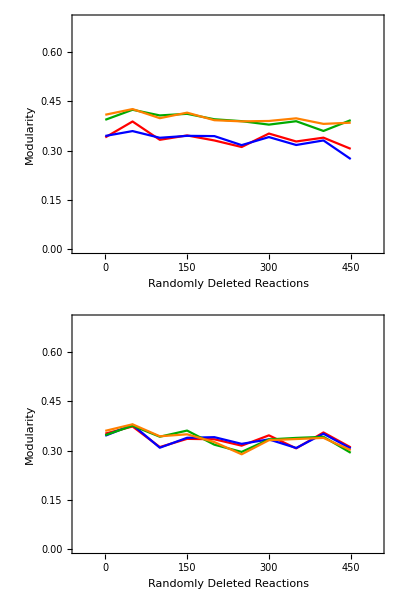
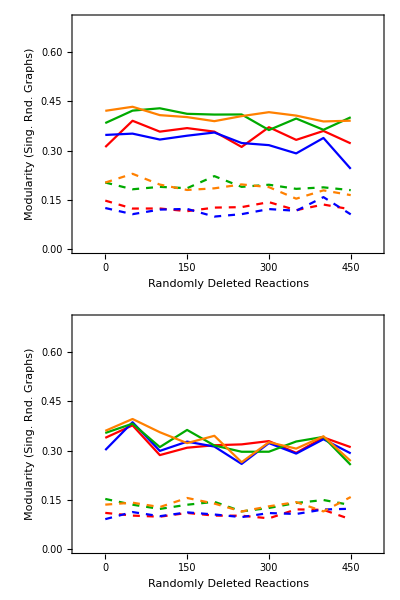
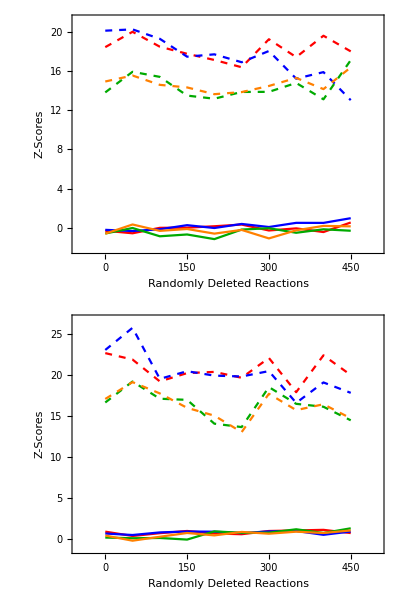

```mathematica
padding=38;
modularityplotrange={0,0.7};
xaxisplotrange={-50,500};
Row[{
Column[{ListLinePlot[modularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[modularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[singlerandommodularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores12m1p1,zscores12m2m4,zscores12m4p4,zscores12p2p4}],1]}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores32m1p1,zscores32m2m4,zscores32m4p4,zscores32p2p4}],1]}]}]
,Column[{LineLegend[{Darker@Green,Blue,Orange,Red},{"(-4,-2)","(-1,1)","(2,4)","(-4,4)"},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Objective Function\nCoefficient Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

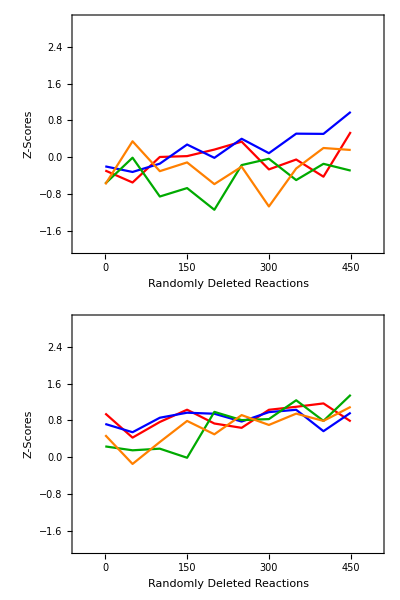

```mathematica
Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}]}]
```

Objective Function Intervals: (-20,20), (-5,5), (-10,-20), (10,20)

Data Input

```mathematica
modularityvalues12m4p4=Import["plot_values/half_obj-funcs/(-20,20)-modularityvalues-fss.mx"];
modularityvalues12m1p1=Import["plot_values/half_obj-funcs/(-5,5)-modularityvalues-fss.mx"];
modularityvalues12m2m4=Import["plot_values/half_obj-funcs/(-10,-20)-modularityvalues-fss.mx"];
modularityvalues12p2p4=Import["plot_values/half_obj-funcs/(10,20)-modularityvalues-fss.mx"];

modularityvalues32m4p4=Import["plot_values/half_obj-funcs/(-20,20)-modularityvalues-fbs.mx"];
modularityvalues32m1p1=Import["plot_values/half_obj-funcs/(-5,5)-modularityvalues-fbs.mx"];
modularityvalues32m2m4=Import["plot_values/half_obj-funcs/(-10,-20)-modularityvalues-fbs.mx"];
modularityvalues32p2p4=Import["plot_values/half_obj-funcs/(10,20)-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues12m4p4=Import["plot_values/half_obj-funcs/(-20,20)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m4p4=Import["plot_values/half_obj-funcs/(-20,20)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m1p1=Import["plot_values/half_obj-funcs/(-5,5)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m1p1=Import["plot_values/half_obj-funcs/(-5,5)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m2m4=Import["plot_values/half_obj-funcs/(-10,-20)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m2m4=Import["plot_values/half_obj-funcs/(-10,-20)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12p2p4=Import["plot_values/half_obj-funcs/(10,20)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12p2p4=Import["plot_values/half_obj-funcs/(10,20)-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues32m4p4=Import["plot_values/half_obj-funcs/(-20,20)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m4p4=Import["plot_values/half_obj-funcs/(-20,20)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m1p1=Import["plot_values/half_obj-funcs/(-5,5)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m1p1=Import["plot_values/half_obj-funcs/(-5,5)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m2m4=Import["plot_values/half_obj-funcs/(-10,-20)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m2m4=Import["plot_values/half_obj-funcs/(-10,-20)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32p2p4=Import["plot_values/half_obj-funcs/(10,20)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32p2p4=Import["plot_values/half_obj-funcs/(10,20)-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores12m4p4=Import["plot_values/half_obj-funcs/(-20,20)-zscores-fss.mx"];
zscores12m1p1=Import["plot_values/half_obj-funcs/(-5,5)-zscores-fss.mx"];
zscores12m2m4=Import["plot_values/half_obj-funcs/(-10,-20)-zscores-fss.mx"];
zscores12p2p4=Import["plot_values/half_obj-funcs/(10,20)-zscores-fss.mx"];

zscores32m4p4=Import["plot_values/half_obj-funcs/(-20,20)-zscores-fbs.mx"];
zscores32m1p1=Import["plot_values/half_obj-funcs/(-5,5)-zscores-fbs.mx"];
zscores32m2m4=Import["plot_values/half_obj-funcs/(-10,-20)-zscores-fbs.mx"];
zscores32p2p4=Import["plot_values/half_obj-funcs/(10,20)-zscores-fbs.mx"];
```

```mathematica
deletionrange=Range[0,450,50]
```

{0,50,100,150,200,250,300,350,400,450}

```mathematica
modularityvalues12={Thread[{deletionrange,modularityvalues12m4p4}],Thread[{deletionrange,modularityvalues12m1p1}],Thread[{deletionrange,modularityvalues12m2m4}],Thread[{deletionrange,modularityvalues12p2p4}]};
modularityvalues32={Thread[{deletionrange,modularityvalues32m4p4}],Thread[{deletionrange,modularityvalues32m1p1}],Thread[{deletionrange,modularityvalues32m2m4}],Thread[{deletionrange,modularityvalues32p2p4}]};
```

```mathematica
singlerandommodularityvalues12={Thread[{deletionrange,singlerandomerdrenmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12p2p4}]};
singlerandommodularityvalues32={Thread[{deletionrange,singlerandomerdrenmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32p2p4}]};
```

```mathematica
zscores12={Thread[{deletionrange,zscores12m4p4[[All,1]]}],Thread[{deletionrange,zscores12m4p4[[All,2]]}],Thread[{deletionrange,zscores12m1p1[[All,1]]}],Thread[{deletionrange,zscores12m1p1[[All,2]]}],Thread[{deletionrange,zscores12m2m4[[All,1]]}],Thread[{deletionrange,zscores12m2m4[[All,2]]}],Thread[{deletionrange,zscores12p2p4[[All,1]]}],Thread[{deletionrange,zscores12p2p4[[All,2]]}]};
zscores32={Thread[{deletionrange,zscores32m4p4[[All,1]]}],Thread[{deletionrange,zscores32m4p4[[All,2]]}],Thread[{deletionrange,zscores32m1p1[[All,1]]}],Thread[{deletionrange,zscores32m1p1[[All,2]]}],Thread[{deletionrange,zscores32m2m4[[All,1]]}],Thread[{deletionrange,zscores32m2m4[[All,2]]}],Thread[{deletionrange,zscores32p2p4[[All,1]]}],Thread[{deletionrange,zscores32p2p4[[All,2]]}]};
```

Plots

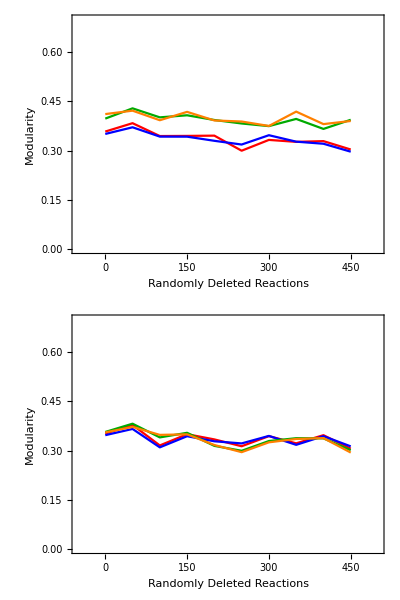
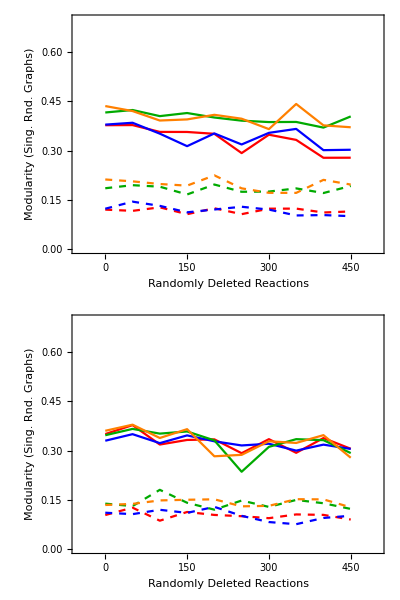
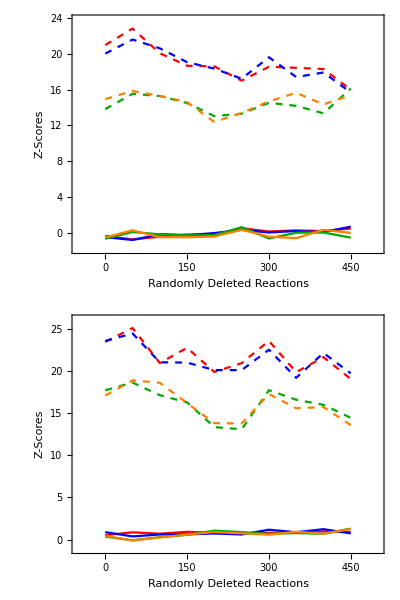

```mathematica
padding=38;
modularityplotrange={0,0.7};
xaxisplotrange={-50,500};
Row[{
Column[{ListLinePlot[modularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[modularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[singlerandommodularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores12m1p1,zscores12m2m4,zscores12m4p4,zscores12p2p4}],1]}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores32m1p1,zscores32m2m4,zscores32m4p4,zscores32p2p4}],1]}]}]
,Column[{LineLegend[{Darker@Green,Blue,Orange,Red},{"(-20,-10)","(-5,5)","(10,20)","(-20,20)"},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Objective Function\nCoefficient Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

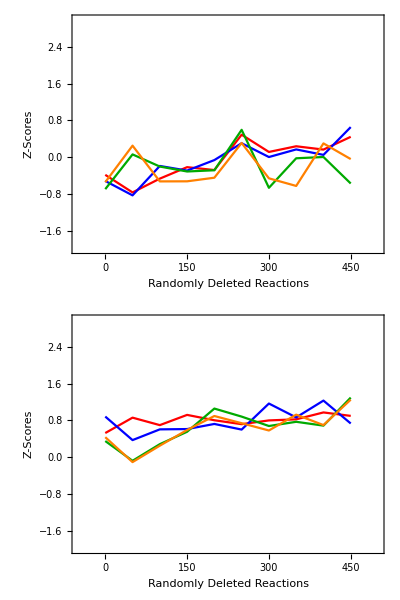

```mathematica
Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}]}]
```

Objective Function Terms Reduced by 75%

Objective Function Intervals: (-4,4), (-1,1), (-2,-4), (2,4)

Data Input

```mathematica
modularityvalues12m4p4=Import["plot_values/75per_dec_obj-funcs/(-4,4)-modularityvalues-fss.mx"];
modularityvalues12m1p1=Import["plot_values/75per_dec_obj-funcs/(-1,1)-modularityvalues-fss.mx"];
modularityvalues12m2m4=Import["plot_values/75per_dec_obj-funcs/(-2,-4)-modularityvalues-fss.mx"];
modularityvalues12p2p4=Import["plot_values/75per_dec_obj-funcs/(2,4)-modularityvalues-fss.mx"];

modularityvalues32m4p4=Import["plot_values/75per_dec_obj-funcs/(-4,4)-modularityvalues-fbs.mx"];
modularityvalues32m1p1=Import["plot_values/75per_dec_obj-funcs/(-1,1)-modularityvalues-fbs.mx"];
modularityvalues32m2m4=Import["plot_values/75per_dec_obj-funcs/(-2,-4)-modularityvalues-fbs.mx"];
modularityvalues32p2p4=Import["plot_values/75per_dec_obj-funcs/(2,4)-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues12m4p4=Import["plot_values/75per_dec_obj-funcs/(-4,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m4p4=Import["plot_values/75per_dec_obj-funcs/(-4,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m1p1=Import["plot_values/75per_dec_obj-funcs/(-1,1)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m1p1=Import["plot_values/75per_dec_obj-funcs/(-1,1)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m2m4=Import["plot_values/75per_dec_obj-funcs/(-2,-4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m2m4=Import["plot_values/75per_dec_obj-funcs/(-2,-4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12p2p4=Import["plot_values/75per_dec_obj-funcs/(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12p2p4=Import["plot_values/75per_dec_obj-funcs/(2,4)-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues32m4p4=Import["plot_values/75per_dec_obj-funcs/(-4,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m4p4=Import["plot_values/75per_dec_obj-funcs/(-4,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m1p1=Import["plot_values/75per_dec_obj-funcs/(-1,1)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m1p1=Import["plot_values/75per_dec_obj-funcs/(-1,1)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m2m4=Import["plot_values/75per_dec_obj-funcs/(-2,-4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m2m4=Import["plot_values/75per_dec_obj-funcs/(-2,-4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32p2p4=Import["plot_values/75per_dec_obj-funcs/(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32p2p4=Import["plot_values/75per_dec_obj-funcs/(2,4)-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores12m4p4=Import["plot_values/75per_dec_obj-funcs/(-4,4)-zscores-fss.mx"];
zscores12m1p1=Import["plot_values/75per_dec_obj-funcs/(-1,1)-zscores-fss.mx"];
zscores12m2m4=Import["plot_values/75per_dec_obj-funcs/(-2,-4)-zscores-fss.mx"];
zscores12p2p4=Import["plot_values/75per_dec_obj-funcs/(2,4)-zscores-fss.mx"];

zscores32m4p4=Import["plot_values/75per_dec_obj-funcs/(-4,4)-zscores-fbs.mx"];
zscores32m1p1=Import["plot_values/75per_dec_obj-funcs/(-1,1)-zscores-fbs.mx"];
zscores32m2m4=Import["plot_values/75per_dec_obj-funcs/(-2,-4)-zscores-fbs.mx"];
zscores32p2p4=Import["plot_values/75per_dec_obj-funcs/(2,4)-zscores-fbs.mx"];
```

```mathematica
deletionrange=Range[0,450,50]
```

{0,50,100,150,200,250,300,350,400,450}

```mathematica
modularityvalues12={Thread[{deletionrange,modularityvalues12m4p4}],Thread[{deletionrange,modularityvalues12m1p1}],Thread[{deletionrange,modularityvalues12m2m4}],Thread[{deletionrange,modularityvalues12p2p4}]};
modularityvalues32={Thread[{deletionrange,modularityvalues32m4p4}],Thread[{deletionrange,modularityvalues32m1p1}],Thread[{deletionrange,modularityvalues32m2m4}],Thread[{deletionrange,modularityvalues32p2p4}]};
```

```mathematica
singlerandommodularityvalues12={Thread[{deletionrange,singlerandomerdrenmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12p2p4}]};
singlerandommodularityvalues32={Thread[{deletionrange,singlerandomerdrenmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32p2p4}]};
```

```mathematica
zscores12={Thread[{deletionrange,zscores12m4p4[[All,1]]}],Thread[{deletionrange,zscores12m4p4[[All,2]]}],Thread[{deletionrange,zscores12m1p1[[All,1]]}],Thread[{deletionrange,zscores12m1p1[[All,2]]}],Thread[{deletionrange,zscores12m2m4[[All,1]]}],Thread[{deletionrange,zscores12m2m4[[All,2]]}],Thread[{deletionrange,zscores12p2p4[[All,1]]}],Thread[{deletionrange,zscores12p2p4[[All,2]]}]};
zscores32={Thread[{deletionrange,zscores32m4p4[[All,1]]}],Thread[{deletionrange,zscores32m4p4[[All,2]]}],Thread[{deletionrange,zscores32m1p1[[All,1]]}],Thread[{deletionrange,zscores32m1p1[[All,2]]}],Thread[{deletionrange,zscores32m2m4[[All,1]]}],Thread[{deletionrange,zscores32m2m4[[All,2]]}],Thread[{deletionrange,zscores32p2p4[[All,1]]}],Thread[{deletionrange,zscores32p2p4[[All,2]]}]};
```

Plots

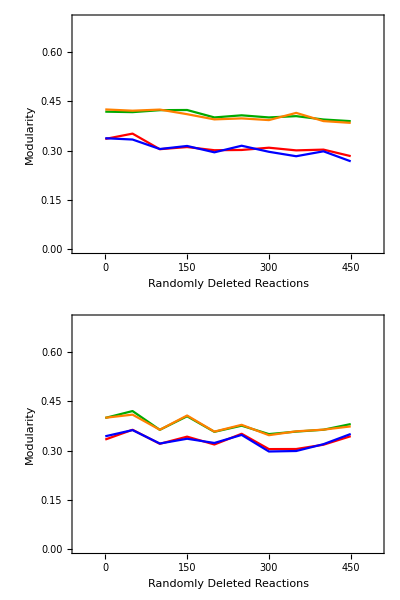
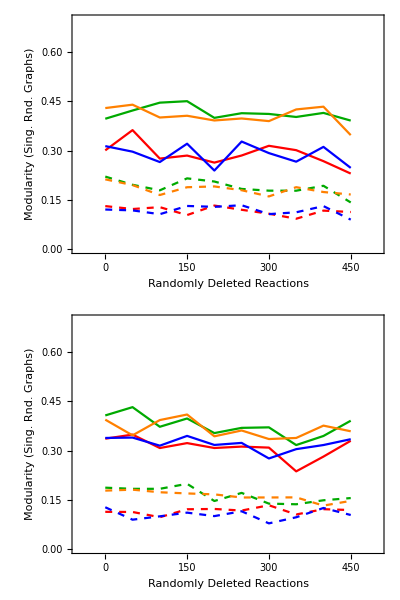
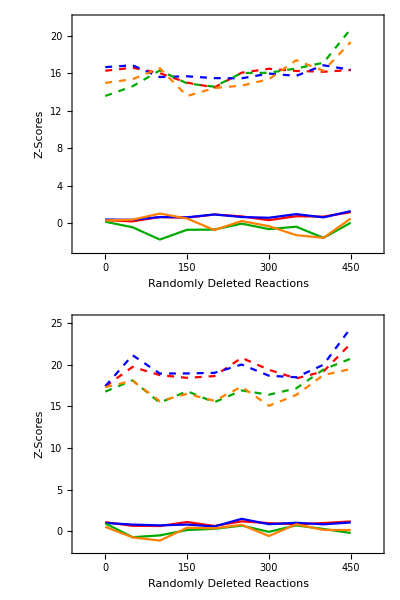

```mathematica
padding=38;
modularityplotrange={0,0.7};
xaxisplotrange={-50,500};
Row[{
Column[{ListLinePlot[modularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[modularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[singlerandommodularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores12m1p1,zscores12m2m4,zscores12m4p4,zscores12p2p4}],1]}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,MinMax[Flatten[{zscores32m1p1,zscores32m2m4,zscores32m4p4,zscores32p2p4}],1]}]}]
,Column[{LineLegend[{Darker@Green,Blue,Orange,Red},{"(-4,-2)","(-1,1)","(2,4)","(-4,4)"},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Objective Function\nCoefficient Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

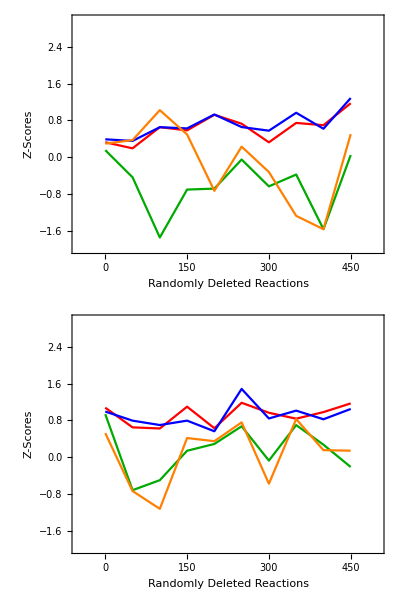

```mathematica
Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}]}]
```